## Signature quantum number

```mathematica
r[spin_]:=Exp[I*π*spin];
```

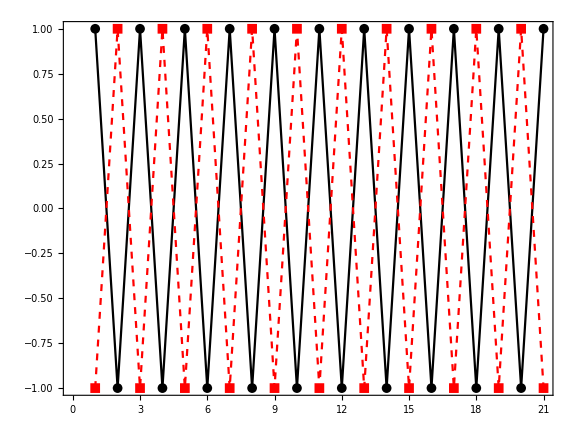

```mathematica
ListPlot[{Table[r[x],{x,0,20,1}],Table[I*r[i],{i,1/2,41/2,1}]},Joined->True,ImageSize->Large,PlotStyle->{{Black},{Red,Dashed}},PlotMarkers->{Automatic,Medium},AspectRatio->0.75,Frame->True,Axes->True,AxesStyle->Thick,FrameStyle->Directive[Black,Thick]]
```

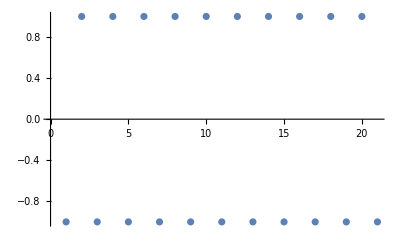

```mathematica
ListPlot[Table[I*r[i],{i,1/2,41/2,1}]]
```

```mathematica
CoordinateTransform["Spherical"->"Cartesian",{R,θ,ϕ}]
```

{R Cos[ϕ] Sin[θ],R Sin[θ] Sin[ϕ],R Cos[θ]}

```mathematica
Exp[-I*π/2]
```

-ⅈ

```mathematica
SphericalHarmonicY[2,2,θ,ϕ]
```

1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2